A decreasing function, divide its evaluation at k-l-1 by its evaluation at k-r.

```mathematica
With[
{k=100},
Table[
(2k-l-1)/(k-l-1)//N,
{l,1,10}]]//TableForm
```

2.02041
2.03093
2.04167
2.05263
2.06383
2.07527
2.08696
2.0989
2.11111
2.1236

```mathematica
With[
{k=100},
Table[
(l+2)/(l+1)r/(r+1)(k-l)/(2k-l)(2k-r+1)/(k-r+1)//N,
{r,1,10},
{l,1,10}]]//TableForm
```

0.746231 | 0.659933 | 0.615482 | 0.587755 | 0.568376 | 0.553756 | 0.542098 | 0.532407 | 0.524084 | 0.516746
1. | 0.884354 | 0.824788 | 0.787631 | 0.761662 | 0.74207 | 0.726448 | 0.713462 | 0.702308 | 0.692475
1.13077 | 1. | 0.932644 | 0.890629 | 0.861264 | 0.839109 | 0.821445 | 0.80676 | 0.794147 | 0.783029
1.21243 | 1.07222 | 1. | 0.954951 | 0.923465 | 0.89971 | 0.88077 | 0.865025 | 0.851501 | 0.83958
1.26963 | 1.1228 | 1.04717 | 1. | 0.967029 | 0.942153 | 0.92232 | 0.905832 | 0.89167 | 0.879187
1.31292 | 1.16108 | 1.08288 | 1.0341 | 1. | 0.974277 | 0.953767 | 0.936717 | 0.922072 | 0.909163
1.34758 | 1.19174 | 1.11147 | 1.0614 | 1.0264 | 1. | 0.978949 | 0.961448 | 0.946417 | 0.933167
1.37656 | 1.21737 | 1.13537 | 1.08422 | 1.04847 | 1.0215 | 1. | 0.982123 | 0.966769 | 0.953234
1.40162 | 1.23953 | 1.15604 | 1.10396 | 1.06756 | 1.0401 | 1.0182 | 1. | 0.984366 | 0.970585
1.42388 | 1.25921 | 1.1744 | 1.12149 | 1.08451 | 1.05662 | 1.03437 | 1.01588 | 1. | 0.986

```mathematica
With[
{k=100},
Table[
(k-l)/(2k-l)(2k-r+1)/(k-r+1)//N,
{r,1,10},
{l,1,10}]]//TableForm
```

0.994975 | 0.989899 | 0.984772 | 0.979592 | 0.974359 | 0.969072 | 0.963731 | 0.958333 | 0.95288 | 0.947368
1. | 0.994898 | 0.989745 | 0.984539 | 0.97928 | 0.973966 | 0.968598 | 0.963173 | 0.957692 | 0.952153
1.00513 | 1. | 0.99482 | 0.989588 | 0.984301 | 0.978961 | 0.973565 | 0.968112 | 0.962603 | 0.957035
1.01036 | 1.00521 | 1. | 0.99474 | 0.989426 | 0.984058 | 0.978634 | 0.973153 | 0.967615 | 0.962018
1.0157 | 1.01052 | 1.00529 | 1. | 0.994658 | 0.989261 | 0.983808 | 0.978299 | 0.972731 | 0.967105
1.02116 | 1.01595 | 1.01069 | 1.00537 | 1. | 0.994574 | 0.989092 | 0.983553 | 0.977955 | 0.972299
1.02673 | 1.02149 | 1.0162 | 1.01086 | 1.00546 | 1. | 0.994488 | 0.988918 | 0.983291 | 0.977604
1.03242 | 1.02715 | 1.02183 | 1.01646 | 1.01103 | 1.00554 | 1. | 0.9944 | 0.988741 | 0.983022
1.03823 | 1.03294 | 1.02759 | 1.02218 | 1.01672 | 1.01121 | 1.00563 | 1. | 0.994309 | 0.988558
1.04418 | 1.03885 | 1.03347 | 1.02803 | 1.02254 | 1.01699 | 1.01139 | 1.00572 | 1. | 0.994216

```mathematica
θ[x_]:=(k+x)/x
```

```mathematica
θ[x]//Expand
```

1+k/x

```mathematica
θ1[x_]:=(1+x)/x
```

```mathematica
θ[x]//Expand
```

1+k/x

```mathematica
(l+2)/(l+1)r/(r+1)
```

```mathematica
θ1[l+1]/θ1[r]
```

((2+l) r)/((1+l) (1+r))

```mathematica
θ[k-(r-1)]/θ[k-l]
```

((k-l) (1+2 k-r))/((2 k-l) (1+k-r))

```mathematica
θ1[l+1]/θ1[r] θ[k-(r-1)]/θ[k-l]==(l+2)/(l+1)r/(r+1)(k-l)/(2k-l)(2k-r+1)/(k-r+1)
```

True

```mathematica
Solve[
{up==n-Γ/2,
down==n/2,
down==η up,
Γ==Ξ n},
{up,down,Γ,η}]
```

{{up→1/2 (2 n-n Ξ),down→n/2,Γ→n Ξ,η→1/(2-Ξ)}}

```mathematica
1/2 (2 n-n Ξ)/n//Simplify
```

1-Ξ/2

```mathematica
Assuming[{Ξ≥0,Ξ≤1},(1-η)^(η-1)/η^η/.η->1/(2-Ξ)//Simplify]
```

-(1-Ξ)^(-1+1/(2-Ξ)) (-2+Ξ)

```mathematica
Assuming[{Ξ≥0,Ξ≤1},((2-Ξ)^(1/(2-Ξ))(1-Ξ)^((Ξ-1)/(Ξ-2)))/(Ξ-2)^((Ξ-1)/(Ξ-2))==(1-η)^(η-1)/η^η/.η->1/(2-Ξ)//Simplify]
```

((-2+Ξ) ((2-Ξ)/(-1+Ξ))^(Ξ/(-2+Ξ))-ⅇ^((ⅈ π)/(-2+Ξ)) (-1+Ξ)) (1-Ξ)^(-1+1/(2-Ξ))==0

```mathematica
Assuming[{Ξ≥0,Ξ≤1},(1-1/(2-Ξ))^(1/(2-Ξ)-1)/(1/(2-Ξ))^(1/(2-Ξ))==(1-η)^(η-1)/η^η/.η->1/(2-Ξ)//Simplify]
```

True

```mathematica
Assuming[{Ξ≥0,Ξ≤1},((2-Ξ)^(1/(2-Ξ))(Ξ-1)^((1-Ξ)/(Ξ-2)))/(Ξ-2)^((1-Ξ)/(Ξ-2))==(1-η)^(η-1)/η^η/.η->1/(2-Ξ)//FullSimplify]
```

True

```mathematica
Assuming[{Ξ≥0,Ξ≤1},((2-Ξ)^(1/(2-Ξ))(Ξ-1)^((1-Ξ)/(Ξ-2)))/(Ξ-2)^((1-Ξ)/(Ξ-2))==(1-η)^(η-1)/η^η/.η->1/(2-Ξ)//FullSimplify]
```

True

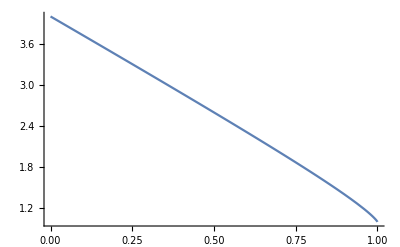

```mathematica
Plot[(((2-Ξ)^(1/(2-Ξ))(Ξ-1)^((1-Ξ)/(Ξ-2)))/(Ξ-2)^((1-Ξ)/(Ξ-2)))^(2-Ξ),{Ξ,0,1}]
```

```mathematica
1/(2-Ξ)-1//Together
```

(1-Ξ)/(-2+Ξ)

```mathematica
Limit[(((2-Ξ)^(1/(2-Ξ))(Ξ-1)^((1-Ξ)/(Ξ-2)))/(Ξ-2)^((1-Ξ)/(Ξ-2)))^(2-Ξ),Ξ->1]
```

1

```mathematica
Limit[(((2-Ξ)^(1/(2-Ξ))(Ξ-1)^((1-Ξ)/(Ξ-2)))/(Ξ-2)^((1-Ξ)/(Ξ-2)))^(2-Ξ),Ξ->0]
```

4

```mathematica
Limit[(((2-Ξ)^(1/(2-Ξ))(Ξ-1)^((1-Ξ)/(Ξ-2)))/(Ξ-2)^((1-Ξ)/(Ξ-2)))^(2-Ξ),Ξ->1/2]//Simplify
```

(3 √3)/2

```mathematica
GoldenRatio
```

```mathematica
(3 √3)/2//N
```

2.59808